# Создание данных для обучения нейронной сети

## 1) График функции 2) график функции с контролируемым шумом

Автор: Климов Олег, студент ФН2-51Б

### Код программы

Исходные данные:

```mathematica
(* Задаваемая функция *)
F[x_]:= Sin[x];

(* Границы графика *) 
GraphicRange := {{-10, 10},{-10, 10}};

(* Количество изображений *)
kolvo := 10;

(* Размер изображения *)
ImgSize := {1000, 1000};

(* Коэффициенты шума *)
NoiseFactor  := 0.01;
TypeNoise := {"•", 20};


(* Путь сохранения чистого графика *) 
TrainFilepath := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_train\\sin\\";
(* Путь сохранения шумного графика *) 
TestFilepath := "C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 5сем\\code\\input\\data_test\\sin\\";
```

Программа:

```mathematica
(* Количество случайных точек *)
numPoints = NoiseFactor * ImgSize[[1]] * ImgSize[[2]] / 100; 

For[i = 1,i < kolvo,i++, 

	(* Задаваемая функция *)
	f[x_]= i F[x] ;
	
	(* Создание чистого графика *)
	
	(* Чистый график *)
	CleanGraphic = Plot[f[x], {x, -10, 10}, AspectRatio -> 1, Axes -> True, PlotRange-> GraphicRange,
	Frame->True,FrameTicks-> None, AxesOrigin -> {0,0}, PlotPoints -> 1000, PlotStyle->Black];
	
	(* Путь сохранения чистого графика *) 
	TrainPath = TrainFilepath <> ToString[i]<>".png";
	
	(* Сохранение чистого графика *)
	Export[TrainPath, CleanGraphic, ImageSize -> ImgSize];
	
	(* Создание шумного графика *)
	xCoords = RandomReal[GraphicRange[[1]] , numPoints];       (* Случайные x-координаты     *)
	yCoords = RandomReal[GraphicRange[[2]] , numPoints];       (* Случайные y-координаты     *)
	points = Transpose[{xCoords, yCoords}];                  (* Объединение координат      *)

	(* Шумный график *) 
	NoizeGraphic= Show[CleanGraphic, ListPlot[points, PlotStyle -> Black, PlotMarkers -> TypeNoise]];
	
	(* Путь сохранения шумного графика *) 
	TestPath = TestFilepath <> ToString[i]<>".png";
	
	(* Сохранение шумного графика *)
	Export[TestPath, NoizeGraphic, ImageSize -> ImgSize];
];
```

Вывод примера результата:

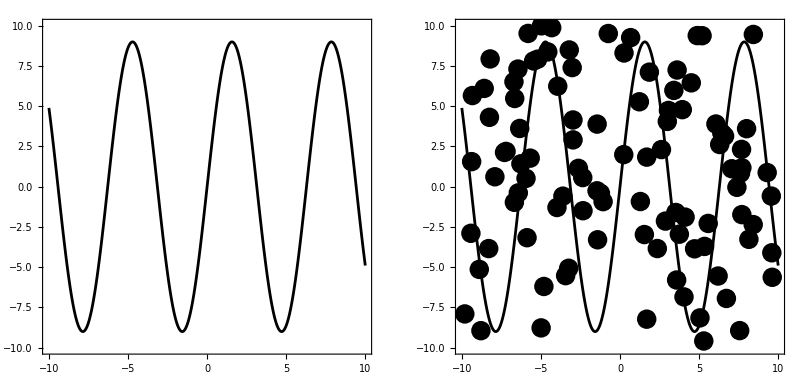

```mathematica
GraphicsRow[{CleanGraphic, NoizeGraphic}, Background -> White]
```